```mathematica
z={0,0.05,0.1,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95}
R=Sqrt[16-((z+3)^2)]
```

{0,0.05,0.1,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95}

{√7,2.58795,2.52784,2.46526,2.33184,2.18575,2.02423,1.84323,1.63631,1.39194,1.08513,0.630476}

```mathematica
circlepoints=Table[{x,(Sqrt[16-((x+3)^2)])+RandomReal[{-0.2,0.2}]},{x,0,1,0.10}]
```

{{0.,2.51764},{0.1,2.70567},{0.2,2.39208},{0.3,2.41347},{0.4,2.02789},{0.5,1.86269},{0.6,1.55354},{0.7,1.69515},{0.8,1.27956},{0.9,0.823463},{1.,0.0158701}}

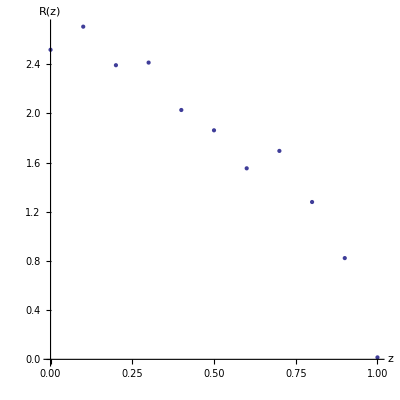

```mathematica
circledata=ListPlot[circlepoints,AxesLabel->{"z","R(z)"},AspectRatio->1]
```

```mathematica
RandomReal[{-0.2,0.2}]
```

0.0362878

```mathematica
model=Sqrt[Rc^2-(x-x0)^2];
fit=FindFit[circlepoints,model,{{Rc,3.9},{x0,0}},x]
```

FindFit::nrlnum: The function value {-2.51764 + 7.56039\ ⅈ, -2.70567 + 7.66724\ ⅈ, -2.39208 + 7.77391\ ⅈ, « 5 », -1.27956 + 8.41049\ ⅈ, -0.823463 + 8.51607\ ⅈ, -0.0158701 + 8.62152\ ⅈ} is not a list of real numbers with dimensions {11} at {Rc, x0} = {2.86653, -8.08557}.

{Rc→2.86653,x0→-8.08557}

```mathematica
hypersphereFit[data_List]:=Module[{mat,rhs,qq,rr,params,cen},mat=Map[Append[#,1]&,data];
rhs=Map[#.#&,data];
{qq,rr}=QRDecomposition[mat];
params=LinearSolve[rr,qq.rhs];
params2={params[[1]],0,params[[3]]};
cen=Drop[params2,-1]/2;
{cen,Sqrt[Last[params]+cen.cen]}]
```

```mathematica
resultfit=hypersphereFit[circlepoints]
```

{{-2.12875,0},3.0456}

```mathematica
m2=resultfit[[1,1]]
Rc2=resultfit[[2]]
```

-2.12875

3.0456

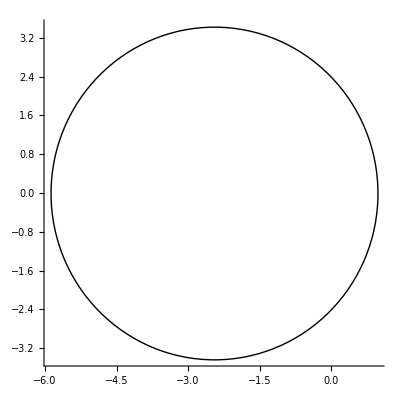

```mathematica
fitcircleplot=Graphics[{Circle[{-2.4563718741049234,0},3.430330974036689]},Axes->True]
```

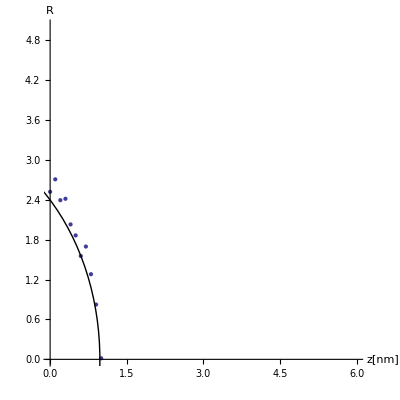

Base radius: 3.0456

```mathematica
Show[circledata,fitcircleplot,AxesLabel->{"z[nm]","R"},AspectRatio->1,PlotRange-> {{0,6},{0,5}}]
Print["Base radius: "<>ToString[resultfit[[2]]]]
```

```mathematica
Θ = 90+(180/π )*ArcSin[m2/Rc2]
```

45.6563

```mathematica
Θ = 90+180/π ArcTan[m2/Sqrt[Rc2^2-m2^2]]
```

45.6563